```mathematica
Integrate[x/β Exp[-x / Sqrt[β]],{x,c,r}]
```

(ⅇ^(-c/(√β)) (c+√β)-ⅇ^(-r/(√β)) (r+√β))/(√β)

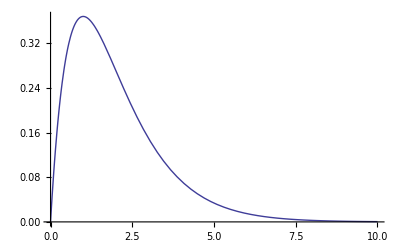

```mathematica
Plot[r Exp[-r],{r,0,10}]
```

```mathematica
Manipulate[
Plot[(1+c) ⅇ^-c-ⅇ^-r (1+r),{r,0,10}],
{c,0,10}]
```

```mathematica
(1+c) ⅇ^-c-ⅇ^-r (1+r)  /. c-> 0
```

1-ⅇ^-r (1+r)